```mathematica
V[r_]:=1/r;
```

```mathematica
energyh=27.211385;
```

```mathematica
me=1;
mp=1836.152674;
μ=(me mp)/(me+mp)
```

0.999456

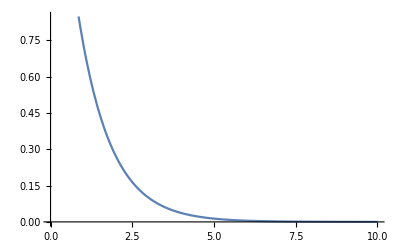

-13.5983

```mathematica
{vals,vecs}=SortBy[Transpose[NDEigensystem[{-1/(2μ)Laplacian[u[x],{x}]-V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}]],First][[1]];
Plot[vecs[x]/x,{x,0,10}]
energyh vals
```

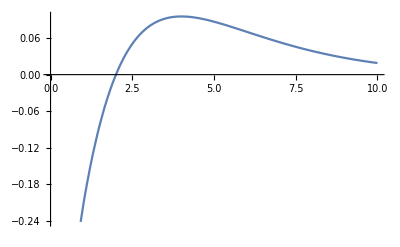

-3.39922

```mathematica
{vals,vecs}=SortBy[Transpose[NDEigensystem[{-1/(2μ)Laplacian[u[x],{x}]-V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}]],First][[2]];
Plot[vecs[x]/x,{x,0,10}]
energyh vals
```

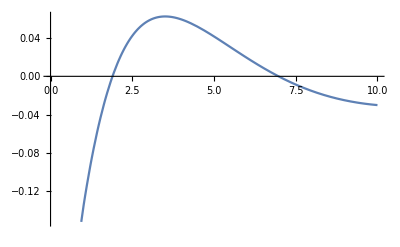

-1.35704

```mathematica
{vals,vecs}=SortBy[Transpose[NDEigensystem[{-1/(2μ)Laplacian[u[x],{x}]-V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}]],First][[3]];
Plot[vecs[x]/x,{x,0,10}]
energyh vals
```

```mathematica
redbohr=1/μ 5.2917721067 10^-11;
e=1.602176621 10^-19;
eps=8.85418782 10^-12;
```

```mathematica
encheckev[n_]:=-e/(4π eps)1/(2 redbohr)1/n^2
```

```mathematica
encheckev[1]
```

-13.5983

```mathematica
-13.598287148853919
```

```mathematica
-13.598286644253267
```